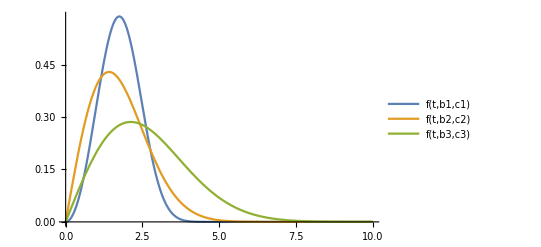

```mathematica
Clear[b1,c1,b2,c2,b3,c3,b4,c4,f,b,c,t];
b1=3; b2=2; b3=2; 
c1=2; c2=2; c3=3;
(*1. Функция плотности распределения Вейбулла f(t) *)
f[t_,b_,c_] := b/c(t/c)^(b-1)*E^(-(t/c)^b);
(* построение графика плотности распределения *)
Plot[{f[t,b1,c1],f[t,b2,c2],f[t,b3,c3]},{t,0,10},PlotLegends->"Expressions"]
```

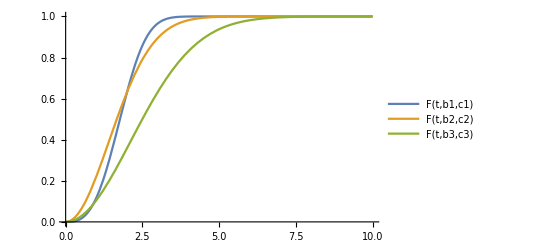

```mathematica
(* 2. Функция распределения Вейбулла F(t) *)
Clear[F,t,b,c];
F[t_,b_,c_] := 1-E^(-(t/c)^b);
(* построение графика распределения *)
Plot[{F[t,b1,c1],F[t,b2,c2],F[t,b3,c3]},{t,0,10},PlotLegends->"Expressions"]
```

```mathematica
(* 3. Начальные моменты *)
Clear[α1,α2,α3,M1,M2];
α1[b_,c_]:=Integrate[t*f[t,b,c],{t,0,Infinity}];          (*Первый начальный момент*)
α2[b_,c_]:=Integrate[t^2*f[t,b,c],{t,0,Infinity}];     (*Второй начальный момент*)
α3[b_,c_]:=Integrate[t^3*f[t,b,c],{t,0,Infinity}];   (*Третий начальный момент*)
(* 4. Математическое ожидание ( 1-ый начальный момент ) *)
M1:=α1 ;
N[M1[b1,c1]]
N[M1[b2,c2]]
N[M1[b3,c3]]
```

1.78596

1.77245

2.65868

```mathematica
M2[b_,c_]:=c*Gamma[1+1/b];
N[M2[b1,c1]]
N[M2[b2,c2]]
N[M2[b3,c3]]
```

1.78596

1.77245

2.65868

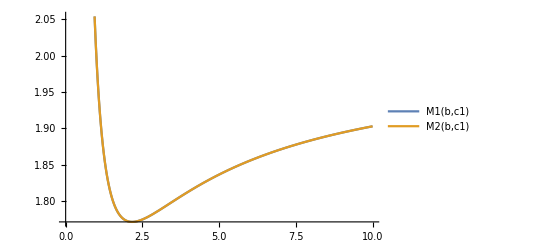

```mathematica
(* построение графика математического ожидания *)
(* зависимость от параметра b *)
Plot[{M1[b,c1],M2[b,c1]},{b,0,10},PlotLegends->"Expressions"]
```

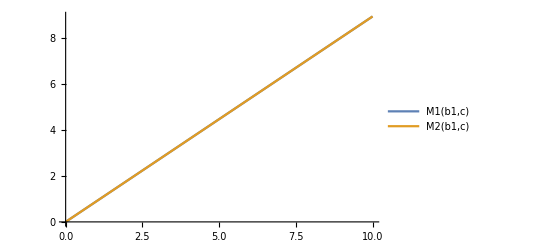

```mathematica
(* зависимость от параметра с *)
Plot[{M1[b1,с],M2[b1,с]},{с,0,10},PlotLegends->"Expressions"]
```

```mathematica
(* 7. Дисперсия ( второй центральный момент ) *)
Clear[D1,D2];
D1[b_,c_]:=α2[b,c]-(α1[b,c])^2;
N[D1[b1,c1]]
N[D1[b2,c2]]
N[D1[b3,c3]]
```

0.421332

0.858407

1.93142

```mathematica
D2[b_,c_]:=c^2*(Gamma[1+2/b]-(Gamma[1+1/b])^2);
N[D2[b1,c1]]
N[D2[b2,c2]]
N[D2[b3,c3]]
```

0.421332

0.858407

1.93142

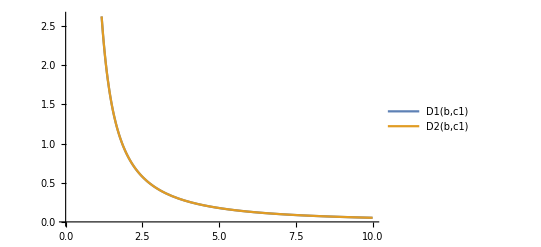

```mathematica
Plot[{D1[b,c1],D2[b,c1]},{b,0,10},PlotLegends->"Expressions"]
```

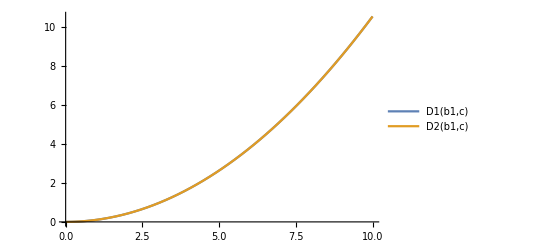

```mathematica
Plot[{D1[b1,с],D2[b1,с]},{с,0,10},PlotLegends->"Expressions"]
```

```mathematica
(* 8. Среднеквадратическое отклонение *)
Clear[σ,μ3,S];
σ[b_,c_]:=Sqrt[D1[b,c]];
N[σ[b1,c1]]
N[σ[b2,c2]]
N[σ[b3,c3]]
```

0.649101

0.926503

1.38975

```mathematica
(* 9. Коэффициент асимметрии *)
μ3[b_,c_]:=(2*(α1[b,c])^3)-3*α1[b,c]*α2[b,c]+α3[b,c];  (* Третий центральный момент *)
N[μ3[b1,c1]]
N[μ3[b2,c2]]
N[μ3[b3,c3]]
```

0.0459739

0.501933

1.69402

```mathematica
S[b_,c_]=μ3[b,c]/(σ[b,c])^3;
N[S[b1,c1]]
N[S[b2,c2]]
N[S[b3,c3]]
```

0.168103

0.631111

0.631111

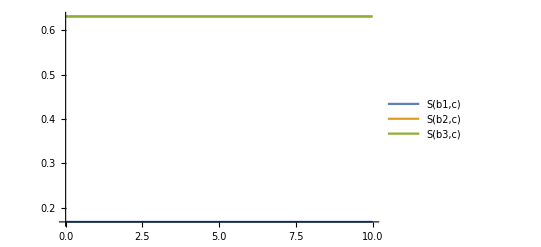

```mathematica
Plot[{S[b1,с],S[b2,с],S[b3,с]},{с,0,10},PlotLegends->"Expressions"]
```

```mathematica
Plot[{S[b,с1],S[b,с2],S[b,с3]},{b,0,10},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
(*5. Мода*)
Clear[Mo1,Mo2,Mo3,Df,Me1,Me2,Me3];
Df[b_,c_]:=Dt[f[t,b,c],t];
Mo1=First[Select[t/.N[Solve[Df[b1,c1]==0,t,Reals]],#>0  And #<10&]]
Mo2=First[Select[t/.N[Solve[Df[b2,c2]==0,t,Reals]],#>0  And #<10&]]
Mo3=First[Select[t/.N[Solve[Df[b3,c3]==0,t,Reals]],#>0  And #<10&]]
```

1.74716

1.41421

2.12132

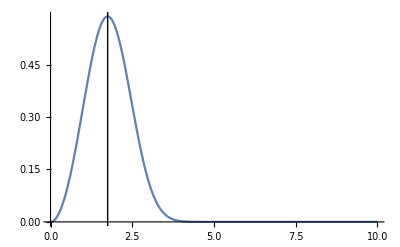

```mathematica
Plot[{f[t,b1,c1]},{t,0,10},Epilog->Line[{{Mo1,-1},{Mo1,1}},VertexColors->{Red, Green}],PlotLegends->"Expressions"]
```

```mathematica
(*6.Медиана*)
```

```mathematica
Me1=First[Select[t/.N[Solve[F[t,b1,c1]==1/2,t,Reals]],#>0  And #<10&]]
Me2=First[Select[t/.N[Solve[F[t,b2,c2]==1/2,t,Reals]],#>0  And #<10&]]
Me3=First[Select[t/.N[Solve[F[t,b3,c3]==1/2,t,Reals]],#>0  And #<10&]]
```

1.76999

1.66511

2.49766

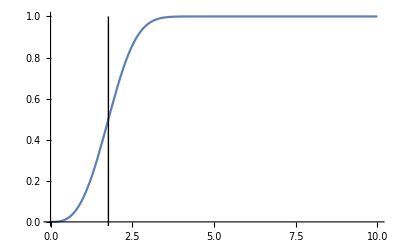

```mathematica
Plot[{F[t,b1,c1]},{t,0,10},Epilog->Line[{{Me1,-1},{Me1,1}},VertexColors->{Red, Green}],PlotLegends->"Expressions"]
```